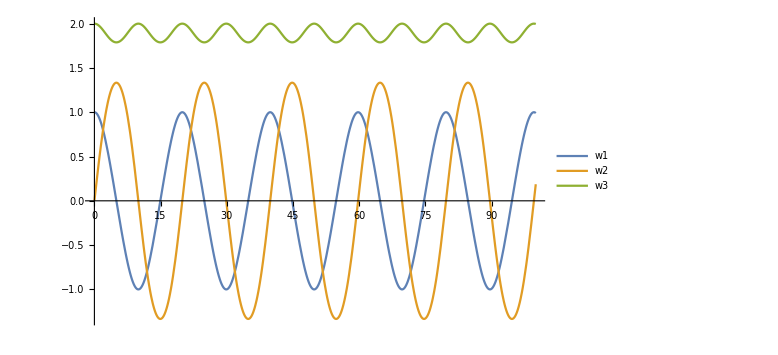

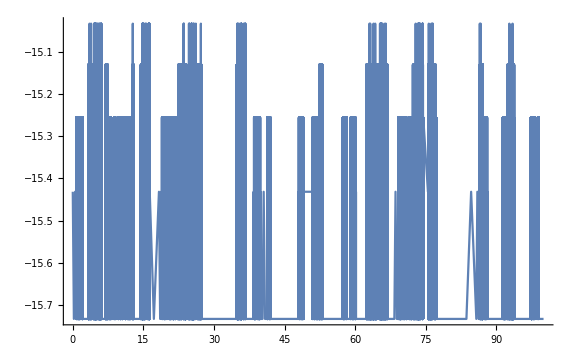

```mathematica
I1 = 0.8; 
I2 = 0.9; 
I3 = 1.; 
w1zero = 1.; 
w2zero = 0.; 
w3zero = 2.; 
tau := t*Sqrt[((I3 - I2)*(M^2 - 2*Energ*I1))/(I1*I2*I3)]
ksqrd = ((I2 - I1)*(2*Energ*I3 - M^2))/((I3 - I2)*(M^2 - 2*Energ*I1)); 
w1[t_] := Sqrt[(2*Energ*I3 - M^2)/(I1*(I3 - I1))]*JacobiCN[tau, ksqrd]
w2[t_] := Sqrt[(2*Energ*I3 - M^2)/(I2*(I3 - I2))]*JacobiSN[tau, ksqrd]
w3[t_] := Sqrt[(-2*Energ*I1 + M^2)/(I3*(I3 - I1))]*JacobiDN[tau, ksqrd]
Energ = 0.5*(w1zero^2*I1 + w2zero^2*I2 + w3zero^2*I3); 
M = Sqrt[w1zero^2*I1^2 + w2zero^2*I2^2 + w3zero^2*I3^2]; 
Plot[{w1[t], w2[t], w3[t]}, {t, 0, 100}, PlotLegends -> {"w1", "w2", "w3"}, ImageSize -> Large, PerformanceGoal -> "Quality"]
Energfunc[t_] := 0.5*(w1[t]^2*I1 + w2[t]^2*I2 + w3[t]^2*I3)
Plot[Log10[Abs[(Energfunc[t] - Energ)/Energ]], {t, 0, 100}, PerformanceGoal -> "Quality", MaxRecursion -> 15, ImageSize -> Large]
```

```mathematica
(*Jacobi' s solution is an analytical solution to Euler' s equations, which has no error.
The numerical implementation of the analytical solution,particularly the Jacobi elliptical functions, however, manifests some
error due to the computer.
Essentially, this is due to the fact that digital computers have magnitude and precision limits in their ability to represent numbers.
Furthermore, Mathematica functions are really optimized to evaluate Jacobi' s elliptic functions,so our error appears to be a roundoff error. 
As a result,our error is caused by our machine' s precision error which is fixed to 10^(-16).*)
```